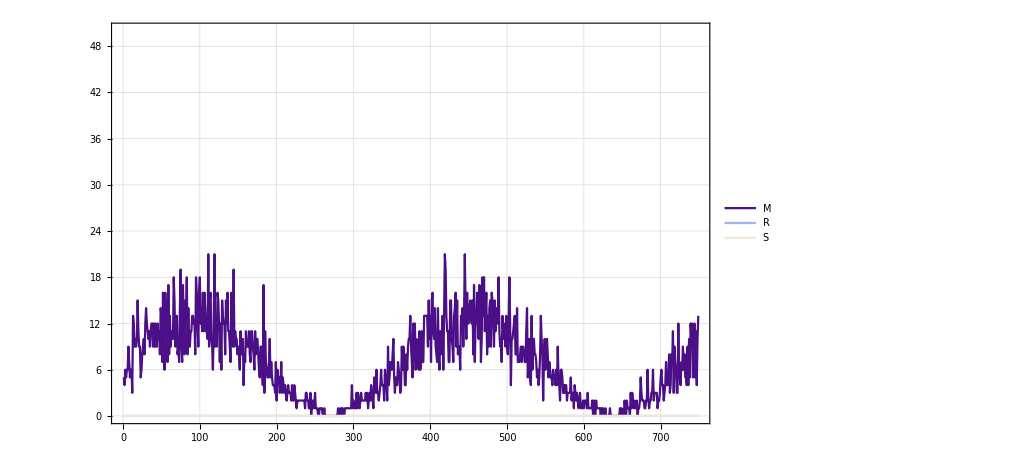
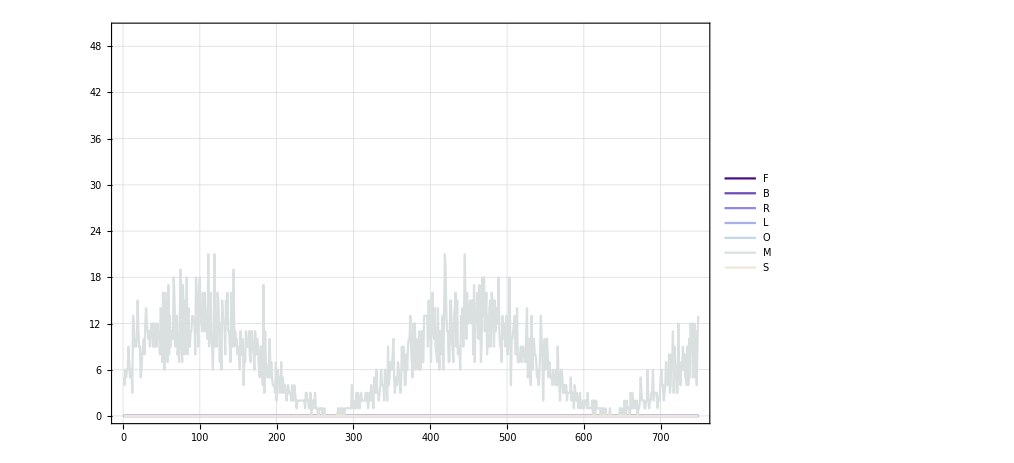
Male | -Graphics-
Female | -Graphics-

/Users/sanchez.hmsc/Documents/GitHub/MASH-Main/MASH-dev/HectorSanchez/VectorControl/Debug/SwarmSprayFull.png

```mathematica
(*Import and Setup Data*)
scenarioName="SwarmSprayFull";
folder=NotebookDirectory[]<>"Debug/Mosquito/";
raw={mRaw,fRaw}=Import[(folder<>#)]&/@{"MaleMosquitoPop_Run1.csv","FemaleMosquitoPop_Run1.csv"};
head={mHead,fHead}=(#[[1,2;;All]])&/@{mRaw,fRaw};
data={mData,fData}=(#[[2;;All,2;;All]])&/@{mRaw,fRaw};
(*Plots*)
plots=ListLinePlot[#[[1]]//Transpose,
PlotRange->{0,50},
Frame->True,
FrameStyle->Directive[Gray,Thick],
GridLines->Automatic,
PlotLegends->#[[2]],
PlotStyle->"LakeColors",
ImageSize->750
]&/@Transpose[{data,head}];
grid=Grid[{Rotate[Style[#,30],90Degree]&/@{"Male","Female"},plots}//Transpose]
(*Export*)
Export[NotebookDirectory[]<>"Debug/"<>scenarioName<>".png",grid,ImageResolution->500]
```